```mathematica
Quit[]
```

# Box with two massive lines

Here we would like to solve the system of differential equation for the topology A16W, i.e. a box integral where two lines have an imaginary mass. In this case we have 8 different master integrals and 2 kinematics invariant (namely s=s12 and t=s13). We have also a parametric dependence of the equations from m_W.

### Import the package and the system of differential equations

```mathematica
SetDirectory[NotebookDirectory[]];
<<../SeaSyde.m
```

+++++ SeaSyde` +++++
Version 1.1.0

SeaSyde is a package for solving the system of differential equation associated to the Master Integrals of a given topology.

For any question or comment, please contact: 
[T. Armadillo](mailto:tommaso.armadillo@uclouvain.be), [R. Bonciani](mailto:roberto.bonciani@roma1.infn.it), [S. Devoto](mailto:simone.devoto@unimi.it), [N. Rana](mailto:narayan.rana@unimi.it) or [A. Vicini](mailto:alessandro.vicini@mi.infn.it).

For the latest version please see the [GitHub repository](https://github.com/TommasoArmadillo/SeaSyde).

```mathematica
dir = "EquationsAndBC/BoxDiagram/";

BoundaryConditions= ReadFrom[dir<>"BoxDiagramBC.m"];
Equations=ReadFrom[dir<>"BoxDiagramEquations.m"];

MasterIntegrals:={j[A16w, 0, 0, 1, 0][s12,s13],j[A16w, 0, 1, 0, 1][s12,s13],j[A16w, 1, 0, 1, 0][s12,s13],j[A16w, 0, 1, 1, 1][s12,s13],j[A16w, 1, 0, 1, 1][s12,s13],j[A16w, 1, 1, 0, 1][s12,s13],j[A16w, 1, 1, 1,0][s12,s13],j[A16w, 1, 1, 1, 1][s12,s13]};
PointBC={-mW^2,-mW^2};
```

SeaSyde: File EquationsAndBC/BoxDiagram/BoxDiagramBC.m has been correctly read.

SeaSyde: File EquationsAndBC/BoxDiagram/BoxDiagramEquations.m has been correctly read.

### Configure and setup the package

```mathematica
ConfigurationBoxDiagram={
EpsilonOrder->2,
ExpansionOrder->50
};
UpdateConfiguration[ConfigurationBoxDiagram]
SetSystemOfDifferentialEquation[Equations,BoundaryConditions,MasterIntegrals,{s12+I δ,s13+I δ},PointBC,{mW->1}]
```

SeaSyde: Updated EpsilonOrder parameter, new value -> 2

SeaSyde: Updated ExpansionOrder parameter, new value -> 50

SeaSyde: There are 2 kinematics variables {s12,s13}

SeaSyde: The Feynman prescriptions for the variables are {ⅈ δ,ⅈ δ}

SeaSyde: There are 8 Master Integrals

SeaSyde: The boundary conditions are imposed in {s12==-1.,s13==-1.}

SeaSyde: The boundary conditions are given as precise value of the solution.

SeaSyde: There are 16 equations and 8 boundary conditions

SeaSyde: The possible singularities for the kinematics variables {s12,s13} are respectively {{0.,4.,4.+4./s13,-1. s13},{4./(-4.+s12),-1. s12,0.,-1.}}

SeaSyde: The system of differential equation has been set and expanded in ϵ

Note that the boundary conditions are obtained for m_W=1, hence the choice of {m_W→1} in the parameters field is somewhat forced.

### Comparison Log/Taylor

We can compare the logarithmic expansion against the Taylor one.

SeaSyde: Updated EpsilonOrder parameter, new value -> 2

SeaSyde: Updated ExpansionOrder parameter, new value -> 75

SeaSyde: Updated LogarithmicExpansion parameter, new value -> True

SeaSyde: There are 2 kinematics variables {s12,s13}

SeaSyde: The Feynman prescriptions for the variables are {ⅈ δ,ⅈ δ}

SeaSyde: There are 8 Master Integrals

SeaSyde: The boundary conditions are imposed in {s12==-1.,s13==-1.}

SeaSyde: The boundary conditions are given as precise value of the solution.

SeaSyde: There are 16 equations and 8 boundary conditions

SeaSyde: The possible singularities for the kinematics variables {s12,s13} are respectively {{0.,4.,4.+4./s13,-1. s13},{4./(-4.+s12),-1. s12,0.,-1.}}

SeaSyde: The system of differential equation has been set and expanded in ϵ

SeaSyde: Moving following these points: {-1.,5.}. NOT avoiding singularities. Here you can see the path in the complex plane for the kinematic variable s12

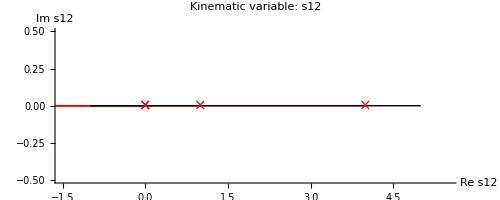

SeaSyde: Moving from the point s12=-1. to s12=5., along the line s12=-1.+6. tInt

SeaSyde: The new point is: s12=0.

SeaSyde: The new point is: s12=0.5

SeaSyde: The new point is: s12=1.

SeaSyde: The new point is: s12=1.5

SeaSyde: The new point is: s12=1.75

SeaSyde: The new point is: s12=2.125

SeaSyde: The new point is: s12=4.

SeaSyde: I arrived at s12=5.. The error estimate is: 0..
Use Solution[] or SolutionValue[] to access the solution, or CreteGraph to plot it.

SeaSyde: Moving following these points: {-1.,-3.}. NOT avoiding singularities. Here you can see the path in the complex plane for the kinematic variable s13

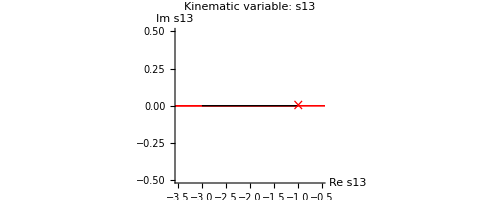

SeaSyde: Moving from the point s13=-1. to s13=-3., along the line s13=-1.-2. tInt

SeaSyde: The new point is: s13=-1.5

SeaSyde: The new point is: s13=-1.75

SeaSyde: The new point is: s13=-2.125

SeaSyde: The new point is: s13=-2.6875

SeaSyde: I arrived at s13=-3.. The error estimate is: 0..
Use Solution[] or SolutionValue[] to access the solution, or CreteGraph to plot it.

Logarithmic expansion time: 71.1652

```mathematica
(* Logarithmic expansion *)
ConfigurationBoxDiagram={
EpsilonOrder->2,
ExpansionOrder->75,
LogarithmicExpansion->True
};
UpdateConfiguration[ConfigurationBoxDiagram]
SetSystemOfDifferentialEquation[Equations,BoundaryConditions,MasterIntegrals,{s12+I δ,s13+I δ},{-1,-1},{mW->1}]
res1=Timing[
TransportBoundaryConditions[{5,-3}];
];
Print[Style["Logarithmic expansion time: "<>ToString[res1[[1]]],Red]];
solLog=SolutionTable[];
```

SeaSyde: Updated EpsilonOrder parameter, new value -> 2

SeaSyde: Updated ExpansionOrder parameter, new value -> 75

SeaSyde: Updated LogarithmicExpansion parameter, new value -> False

SeaSyde: There are 2 kinematics variables {s12,s13}

SeaSyde: The Feynman prescriptions for the variables are {ⅈ δ,ⅈ δ}

SeaSyde: There are 8 Master Integrals

SeaSyde: The boundary conditions are imposed in {s12==-1.,s13==-1.}

SeaSyde: The boundary conditions are given as precise value of the solution.

SeaSyde: There are 16 equations and 8 boundary conditions

SeaSyde: The possible singularities for the kinematics variables {s12,s13} are respectively {{0.,4.,4.+4./s13,-1. s13},{4./(-4.+s12),-1. s12,0.,-1.}}

SeaSyde: The system of differential equation has been set and expanded in ϵ

SeaSyde: Moving following these points: {-1.,-1.+0.5 ⅈ,5.+0.5 ⅈ,5.}, avoiding singularities. Here you can see the path in the complex plane for the kinematic variable s12

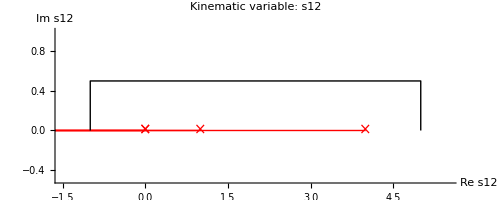

SeaSyde: Moving from the point s12=-1. to s12=-1.+0.5 ⅈ, along the line s12=-1.+(0.+0.5 ⅈ) tInt

SeaSyde: The new point is: s12=-1.+0.5 ⅈ

SeaSyde: Moving from the point s12=-1.+0.5 ⅈ to s12=5.+0.5 ⅈ, along the line s12=(-1.+0.5 ⅈ)+6. tInt

SeaSyde: The new point is: s12=-0.440983+0.5 ⅈ

SeaSyde: The new point is: s12=-0.107642+0.5 ⅈ

SeaSyde: The new point is: s12=0.148086+0.5 ⅈ

SeaSyde: The new point is: s12=0.40882+0.5 ⅈ

SeaSyde: The new point is: s12=0.73175+0.5 ⅈ

SeaSyde: The new point is: s12=1.01546+0.5 ⅈ

SeaSyde: The new point is: s12=1.26558+0.5 ⅈ

SeaSyde: The new point is: s12=1.54865+0.5 ⅈ

SeaSyde: The new point is: s12=1.91981+0.5 ⅈ

SeaSyde: The new point is: s12=2.44327+0.5 ⅈ

SeaSyde: The new point is: s12=3.20698+0.5 ⅈ

SeaSyde: The new point is: s12=3.67572+0.5 ⅈ

SeaSyde: The new point is: s12=3.9737+0.5 ⅈ

SeaSyde: The new point is: s12=4.22404+0.5 ⅈ

SeaSyde: The new point is: s12=4.49799+0.5 ⅈ

SeaSyde: The new point is: s12=4.85084+0.5 ⅈ

SeaSyde: Moving from the point s12=5.+0.5 ⅈ to s12=5., along the line s12=(5.+0.5 ⅈ)-(0.+0.5 ⅈ) tInt

SeaSyde: I arrived at s12=5.. The error estimate is: 0..
Use Solution[] or SolutionValue[] to access the solution, or CreteGraph to plot it.

SeaSyde: Moving following these points: {-1.,-3.}, avoiding singularities. Here you can see the path in the complex plane for the kinematic variable s13

-Graphics-

SeaSyde: Moving from the point s13=-1. to s13=-3., along the line s13=-1.-2. tInt

SeaSyde: The new point is: s13=-1.5

SeaSyde: The new point is: s13=-1.75

SeaSyde: The new point is: s13=-2.125

SeaSyde: The new point is: s13=-2.6875

SeaSyde: I arrived at s13=-3.. The error estimate is: 0..
Use Solution[] or SolutionValue[] to access the solution, or CreteGraph to plot it.

Taylor expansion time: 143.725

```mathematica
(* Taylor expansion *)
ConfigurationBoxDiagram={
EpsilonOrder->2,
ExpansionOrder->75,
LogarithmicExpansion->False
};
UpdateConfiguration[ConfigurationBoxDiagram]
SetSystemOfDifferentialEquation[Equations,BoundaryConditions,MasterIntegrals,{s12+I δ,s13+I δ},{-1,-1},{mW->1}]
res2=Timing[
TransportBoundaryConditions[{5,-3}];
];
Print[Style["Taylor expansion time: "<>ToString[res2[[1]]],Red]];
solTaylor=SolutionTable[];
```

In this case, since the structure of the singularities is not complicate, the logarithmic expansion has better performances, however this is not true in general. For two-loop integrals the Taylor expansion requires, generally, less time. During our tests we also observed that the performances of the logarithmic expansions are much more affected by the number of terms used in the series than the Taylor one. Of course the result does not depend on the expansion we use.

```mathematica
(* Difference *)
solTaylor-solLog//Abs//Max//N
```

3.1796×10^-16